This is me doing stuff

Mass in GeV?

```mathematica
(*Declaring some constants*)
Me=.000511;
Mμ=.1057;
Mτ=1.777;
MW=80.4;
Mu= 0.0023;
Md= 0.0048;
Ms = 0.095;
Mc = 1.4;
Mt = 172;
Mb  = 4.2;
MZ=91;
v=246;
Bem[Mx_]=-11/3;
Bg[Mx_]=7;
taue[Mx_]=4 Me^2/Mx^2;
tauμ[Mx_]=4 Mμ^2/Mx^2;
tauτ[Mx_]= 4 Mτ^2/Mx^2;
tauW[Mx_]=4 MW^2/Mx^2;
tauu[Mx_]=4 Mu^2/Mx^2;
taud[Mx_]=4 Md^2/Mx^2;
taus[Mx_]=4 Ms^2/Mx^2;
tauc[Mx_]=4 Mc^2/Mx^2;
taut[Mx_]=4 Mt^2/Mx^2;
taub[Mx_] =4 Mb^2/Mx^2;
ft[taui_]=Piecewise[{{ArcSin[√(1/taui)]^2,taui≥1},{-1/4 (Log[(1+√(1-taui))/(1-√(1-taui))]-ⅈ π)^2,taui<1}}];
F1[tau1_]=2+3tau1+(3tau1)*(2-tau1) ft[tau1];
F12[tau12_]= -2tau12(1+(1-tau12) ft[tau12]);
SumLoopCorrectionRγ[Mx_]=       F12[taue[Mx]]+F12[tauμ[Mx]]+F12[tauτ[Mx]]+F1[tauW[Mx]] + 3(2/3)^2 F12[tauu[Mx]]+3(-1/3)^2 F12[taud[Mx]]+ 3(2/3)^2 F12[tauc[Mx]]+3(-1/3)^2 F12[taus[Mx]]+ 3(2/3)^2 F12[taut[Mx]]+3(-1/3)^2 F12[taub[Mx]];
SumLoopCorrectionRg[Mx_]=F12[tauu[Mx]]+F12[taud[Mx]]+F12[taus[Mx]]+F12[tauc[Mx]]+F12[taut[Mx]]+F12[taub[Mx]];
Rg[Mx_]=Abs[-Bg[Mx]+1/2 SumLoopCorrectionRg[Mx]]^2/Abs[1/2 SumLoopCorrectionRg[Mx]]^2;
Rγ[Mx_]=Abs[-Bem[Mx]+SumLoopCorrectionRγ[Mx]]^2/Abs[SumLoopCorrectionRγ[Mx]]^2;
Plot[{Rγ[Mx],Rg[Mx]/100},{Mx,20,200},PlotRange ->{{20,200},{0,3}},PlotLegends->"Expressions",Frame->True, AxesOrigin->{20,0},PlotLabel->"Rg and Rγ",Exclusions-> None]
Plot[Rg[Mx]/100,{Mx,200,1000},PlotRange ->{{200,1000},{.4,1.6}},PlotLegends->"Expressions",Frame->True, AxesOrigin->{20,0},PlotLabel ->"Rg",Exclusions-> None]
Plot[{Rg[Mx]*Rγ[Mx]},{Mx,20,200}]
(*Higgs Width Function peices end with H*)
Gμ=1.16637*10^-5;
α=1/128;
αs = .1172;
```

```mathematica
1/16.
```

```mathematica
(v/500.)^4
```

```mathematica
Manipulate[Plot[{Rg[Mx]*Rγ[Mx]*(v/f)^4},{Mx,20,200}],{f,500,1000}]
```

Higgs functions, note change in definition of τ

```mathematica
taueH[Mh_]=Mh^2/(4 Me^2);
tauμH[Mh_]=Mh^2/(4 Mμ^2);
tauτH[Mh_]=Mh^2/(4 Mτ^2);
tauWH[Mh_]=Mh^2/(4 MW^2);
tauuH[Mh_]=Mh^2/(4 Mu^2);
taudH[Mh_]=Mh^2/(4 Md^2);
tausH[Mh_]=Mh^2/(4 Ms^2);
taucH[Mh_]=Mh^2/(4 Mc^2);
tautH[Mh_]=Mh^2/(4 Mt^2);
taubH[Mh_]=Mh^2/(4 Mb^2);
(*f(t) for the Higgs*)
ftH[tauHi_]= Piecewise[{{ArcSin[√tauHi]^2,tauHi ≤ 1},{-1/4(Log[(1+√(1-tauHi^-1))/(1-√(1-tauHi^-1))]-ⅈ*π)^2,tauHi > 1}}];
(*Form Factors for spin 1/2 and spin 1 particles*)
A12H[tauHi_]=2(tauHi+(tauHi-1)*ftH[tauHi])*(tauHi)^-2;
A1H[tauHi_]=-(2(tauHi)^2+3tauHi+3(2tauHi-1)*ftH[tauHi])tauHi^-2;
SumFermionsAndWHiggs[Mh_]=A12H[taueH[Mh]]+A12H[tauμH[Mh]]+A12H[tauτH[Mh]]+A1H[tauWH[Mh]] + 3(2/3)^2 A12H[tauuH[Mh]]+3(-1/3)^2 A12H[taudH[Mh]]+ 3(2/3)^2 A12H[taucH[Mh]]+3(-1/3)^2 A12H[tausH[Mh]]+ 3(2/3)^2*A12H[tautH[Mh]]+3(-1/3)^2 A12H[taubH[Mh]];
(*Width is in GeV*)
WidthHγγ[Mh_]=(Gμ α^2 Mh^3)/(128 √2 π^3)Abs[SumFermionsAndWHiggs[Mh]]^2;
(*Plot is in KeV to match the paper*)
LogLogPlot[Re[WidthHγγ[Mh]]*1000000,{Mh,100,1000},PlotRange ->{{100,1000},{1,150}}PlotLegends->"Expressions",AxesLabel -> {Hx,WidthHγγ},AxesOrigin->{100,0},PlotLabel ->"Width of Higgs Gamma Gamma Decay",Exclusions-> None,MaxRecursion->5]
(*Now here is the width of the Dilaton Gamma Gamma Decay*)
WidthXγγ[Mx_,f_]=Rγ[Mx](v^2/f^2) WidthHγγ[Mx];
Plot3D[WidthXγγ[Mx,f],{f,500,3000},{Mx,0,1000}, ColorFunction->"TemperatureMap",PlotLabel-> "Width of the Dilaton Gamma Gamma Decay",AxesLabel->{"f(GeV)","Mx (GeV)","Γ(X->γγ)(GeV)"},ClippingStyle->Red,Exclusions->None,MaxRecursion->5]
(*This is the Higgs -> gg width Note:Graph is in MeV and function is in GeV*)
SumQuarks[Mh_]=A12H[taubH[Mh]]+A12H[tautH[Mh]];
WidthHgg[Mh_]= (Gμ αs^2 Mh^3)/(36 √2 π^3)Abs[(3/4)* SumQuarks[Mh]]^2;
LogLogPlot[WidthHgg[Mh]*1000,{Mh,100,1000},PlotLegends->"Expressions",AxesLabel -> {Mh,WidthHgg},AxesOrigin->{100,0},PlotLabel ->"Width of Higgs Gluon Gluon Decay" ,Exclusions->None,MaxRecursion->5]
(*Now here is the width of the Dilaton gluon gluon Decay*)
WidthXgg[Mx_,f_]= Rg[Mx](v^2/f^2) WidthHgg[Mx];
Plot3D[WidthXgg[Mx,f],{f,500,3000},{Mx,0,1000}, ColorFunction->"TemperatureMap",PlotLabel-> "Width of the Dilaton Gluon Gluon Decay",AxesLabel->{"f(GeV)","Mx(GeV)","Γ(X->γγ)(GeV)"},Exclusions-> None,MaxRecursion->5]
(* This would be a way to check our contours from paper 7 I dont think this is right*)
σggXγγOVERσggHγγ[f_,Mx_]=Rg[Mx] Rγ[Mx] v^4/f^4;
Plot3D[σggXγγOVERσggHγγ[f,Mx],{Mx,20,200},{f,500,4500},Exclusions-> None,MaxRecursion->5]
ContourPlot[{σggXγγOVERσggHγγ[f,Mx]== 10,σggXγγOVERσggHγγ[f,Mx]== 5,σggXγγOVERσggHγγ[f,Mx]== 2,σggXγγOVERσggHγγ[f,Mx]== 1,σggXγγOVERσggHγγ[f,Mx]== .5,σggXγγOVERσggHγγ[f,Mx]== .2,σggXγγOVERσggHγγ[f,Mx]== .1},{Mx,20,200},{f,500,4500},Exclusions-> None,MaxRecursion->10]
```

This next Section will be the equations for The Higgs Decay to quarks (Hard as Shit)

```mathematica
αsbar[Q_,Nf_]=(12π)/((33-2Nf)Log[Q^2/(.2)^2]);
```

This section is for the Higgs Decay into ZZ and WW for two body decay

```mathematica
xZ[Mh_]=MZ^2/Mh^2;
xW[Mh_]=MW^2/Mh^2;

WidthHZZ[Mh_]=(Gμ Mh^3)/(16 √2 π)1 √(1-4xZ[Mh])(1-4xZ[Mh]+12 xZ[Mh]^2);
WidthHWW[Mh_]=(Gμ Mh^3)/(16 √2 π)2 √(1-4xW[Mh])(1-4xW[Mh]+12 xW[Mh]^2);
Plot[WidthHZZ[Mh],{Mh,20,200}]
Plot[WidthHWW[Mh],{Mh,20,200}]
```

This is for the decay width of a Higgs to a photon and a Z Note the use of the Taus from the dilaton calculations

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

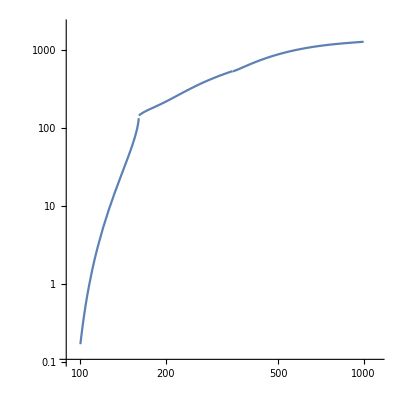

0.00125723

```mathematica
(*Form Factor*)
cw =√(1-.23126);
sw = √0.23126;
λe=4 Me^2/MZ^2;
λμ=4 Mμ^2/MZ^2;
λτ= 4 Mτ^2/MZ^2;
λW=4 MW^2/MZ^2;
λu=4 Mu^2/MZ^2;
λd=4 Md^2/MZ^2;
λs=4 Ms^2/MZ^2;
λc=4 Mc^2/MZ^2;
λt=4 Mt^2/MZ^2;
λb =4 Mb^2/MZ^2;
vfu=2(1/2)^3-4(2/3)sw^2;
vfd=2(1/2)^3-4(-1/3)sw^2;
vfc=2(1/2)^3-4(2/3)sw^2;
vfs=2(1/2)^3-4(-1/3)sw^2;
vft=2(1/2)^3-4(2/3)sw^2;
vfb=2(1/2)^3-4(-1/3)sw^2;
vfe=2(1/2)^3-4(-3/3)sw^2;
vfμ=2(1/2)^3-4(-3/3)sw^2;
vfτ=2(1/2)^3-4(-3/3)sw^2;
g[τ_]=Piecewise[{{√(τ^-1-1)ArcSin[√τ],τ≥1},{(√(1-τ^-1))/2 (Log[(1+√(1-τ^-1))/(1-√(1-τ^-1))]-ⅈ π),τ<1}}];
f[tauHi_]= Piecewise[{{ArcSin[√tauHi]^2,tauHi ≤ 1},{-1/4(Log[(1+√(1-(tauHi^-1)))/(1-√(1-(tauHi^-1)))]-ⅈ*π)^2,tauHi > 1}}];
I1[τ_,λ_]=(τ λ)/(2(τ-λ))+(τ^2 λ^2)/(2(τ-λ)^2)(f[τ^-1]-f[λ^-1])+(τ^2 λ)/(τ-λ)^2(g[τ^-1]-g[λ^-1]);
I2[τ_,λ_]=(-τ λ)/(2(τ-λ))(f[τ^-1]-f[λ^-1]);
A12HZγ[τ_,λ_]=(I1[τ,λ]-I2[τ,λ]);
A1HZγ[τ_,λ_]=cw(4(3-sw^2/cw^2)I2[τ,λ]+((1+2/τ)sw^2/cw^2-(5+2/τ))I1[τ,λ]);
FermionLoop[Mh_] = (- vfe)/cw A12HZγ[taue[Mh],λe]+ (- vfμ)/cw A12HZγ[tauμ[Mh],λμ]+ (- vfτ)/cw A12HZγ[tauτ[Mh],λτ]+ 3((2/3)vfu)/cw A12HZγ[tauu[Mh],λu]+3((-1/3)vfd)/cw A12HZγ[taud[Mh],λd]+3((2/3)vfc)/cw A12HZγ[tauc[Mh],λc]+3((-1/3)vfs)/cw A12HZγ[taus[Mh],λs]+ 3((2/3)vft)/cw A12HZγ[taut[Mh],λt]+3((-1/3)vfb)/cw A12HZγ[taub[Mh],λb];
WidthHZγ[Mh_]=(Gμ^2 MW^2 α Mh^3)/(64 π^4)(1-MZ^2/Mh^2)^3 Abs[FermionLoop[Mh]+A1HZγ[tauW[Mh],λW]]^2;

LogLogPlot[WidthHZγ[Mh]*1000000,{Mh,100,1000},AspectRatio->1]

WidthHZγ[1000]
```

Top Quark Decays for the Higgs Boson With full QCD corrections

Note the use of the top quark  mass of 178 ans the strong coupling constant at .1172

```mathematica
βt[Mh_]=(1-4 178^2/Mh^2)^(1/2);
Atop[β_]=(1-β^2)(4PolyLog[2,(1-β)/(1+β)]+2PolyLog[2,-(1-β)/(1+β)]-3Log[(1+β)/(1-β)]Log[2/(1+β)]-2Log[(1+β)/(1-β)]Log[β])-3β Log[4/(1-β^2)]-4β Log[β];
ΔtH[β_]=1/β Atop[β]+1/(16 β^3)(3+34 β^2-13 β^4)Log[(1+β)/(1-β)]+3/(8 β^2)(7 β^2-1);
WidthHTT[Mh_]=(3Gμ)/(4 √2 π) Mh 178^2 βt[Mh]^3(1+4/3 (.1172)/π ΔtH[βt[Mh]]);
WidthHTT[360]
LogPlot[Re[WidthHTT[Mh]],{Mh,350,700}]
```

```mathematica
ContourPlot[{σggXγγOVERσggHγγ[f,Mx]== 10,σggXγγOVERσggHγγ[f,Mx]== 5,σggXγγOVERσggHγγ[f,Mx]== 2,σggXγγOVERσggHγγ[f,Mx]== 1,σggXγγOVERσggHγγ[f,Mx]== .5,σggXγγOVERσggHγγ[f,Mx]== .2,σggXγγOVERσggHγγ[f,Mx]== .1},{Mx,20,200},{f,500,4500},Exclusions-> None,MaxRecursion->5,PlotLegends->{"10","5","2","1","0.5","0.2","0.1"}]
```

This next section is to compare to the Radion paper fig 9
Rσ is the Ratio of dilaton events to the SM Higgs events
The formula f is a function of F based on the Dilaton mass and the the ratio Rσ
I used the function that we found for Rσ to get F.

```mathematica
F[Rσ_,Mx_] = √((Rg[Mx] v^2 Rγ[Mx])/Rσ);
ContourPlot[{F[Exp@Rσ,Mx]== 500,F[Exp@Rσ,Mx]== 2000,F[Exp@Rσ,Mx]== 5000,F[Exp@Rσ,Mx]== 10000,F[Exp@Rσ,Mx]== 20000},{Mx,20,200},{Rσ,Log[.001],Log[100]},Exclusions->None,MaxRecursion->5,PlotLegends->{500,2000,5000,10000,20000}]
```